```mathematica
scape = Import["/home/nshlapo/Documents/ComplexSocialModeling/sugar_map.txt", "Table"];
```

```mathematica
shape = Dimensions[scape];
initAgents = 300;
initMaxSugar = 5;
shape[[1]]
randomInit = Table[{i,j},{i,shape[[1]]},{j,shape[[2]]}];
```

50

```mathematica
(*agent structure is {x_position, y_position, sugar_wealth}*)
agents = {}
Do[pos=RandomChoice[RandomChoice[randomInit]];
AppendTo[agents,AppendTo[pos, RandomReal[initMaxSugar]]];
  Delete[randomInit,pos];,
 initAgents];
```

{}

Delete::psl: Position specification 1.19091 in … is not a machine-sized integer or a list of machine-sized integers.

Delete::psl: Position specification 2.24616 in … is not a machine-sized integer or a list of machine-sized integers.

Delete::psl: Position specification 3.80585 in … is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

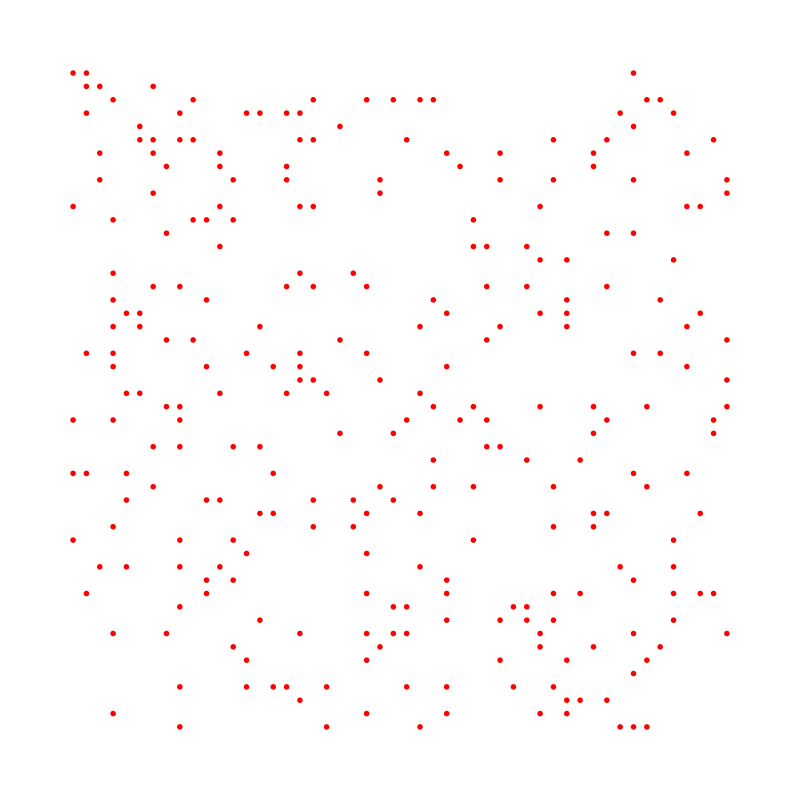

```mathematica
GraphicsGrid[Table[If[MemberQ[agents,{i,j,_}],Graphics[{Red,Disk[]}], ],{i,shape[[1]]},{j,shape[[2]]}], ImageSize->800]
```

```mathematica
(*change agent's coordinates from loc to dest, gain any sugar at dest, 
AgentMove[{loc,dest},
```